```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
(**************Clock times are lists of times when "Dark" session ended and "LED" session began********************)
```

```mathematica
(****Control****)
```

```mathematica
dateMouseListControl={{"011622","Mouse22550"},{"011822","Mouse22550"},{"012322","Mouse22549"},{"012622","Mouse22549"},{"021022","Mouse22549"},{"010522","Mouse22599"},{"021022","Mouse22599"},{"021422","Mouse22599"},{"033122","Mouse22544"},{"040122","Mouse22562"},{"040322","Mouse22544"},{"040322","Mouse22562"},{"032923","Mouse23149"},{"033023","Mouse23128"},{"033123","Mouse23149"}};
```

```mathematica
controlClockTimes={{"12:48 PM","2:19 PM"},{"11:41 AM","2:09 PM"},{"11:59 AM","2:29 PM"},{"10:58 AM","12:45 PM"},{"11:24 AM","1:43 PM"},{"10:53 AM","12:57 PM"},{"10:22 AM","12:40 PM"},{"11:32 AM","1:47 PM"},{"11:37 AM","1:45 PM"},{"2:13 PM","4:14 PM"},{"11:51 AM","1:56 PM"},{"12:46 PM","2:48 PM"},{"12:36 PM","2:29 PM"},{"10:01 AM","12:17 PM"},{"10:27 AM","12:19 PM"}};
```

```mathematica
controlMinutes=Table[QuantityMagnitude[UnitConvert[Differences[Interpreter["Time"]/@controlClockTimes[[n]]][[1]],"Minutes"]],{n,1,Length[controlClockTimes]}];
```

```mathematica
(****V1 eOPN3****)
```

```mathematica
dateMouseListV1axons={{"112221","Mouse22485"},{"112321","Mouse22485"},{"120321","Mouse22485"},{"120821","Mouse22517"},{"121321","Mouse22485"},{"010122","Mouse22547"},{"011222","Mouse22501"},{"011622","Mouse22504"},{"011822","Mouse22504"},{"012322","Mouse22575"},{"012722","Mouse22575"},{"013122","Mouse22504"},{"021022","Mouse22504"},{"021222","Mouse22575"},{"032222","Mouse22506"},{"032622","Mouse22506"},{"040422","Mouse22506"}};
```

```mathematica
v1ClockTimes={{"11:17 AM","1:03 PM"},{"12:49 PM","2:25 PM"},{"10:09 AM","11:35 AM"},{"11:51 AM","1:39 PM"},{"10:28 AM","12:43 PM"},{"11:55 AM","2:25 PM"},{"10:47 AM","12:44 PM"},{"11:22 AM","1:39 PM"},{"10:39 AM","1:20 PM"},{"10:47 AM","1:18 PM"},{"1:56 PM","3:47 PM"},{"3:40 PM","5:08 PM"},{"11:24 AM","1:43 PM"},{"1:17 PM","3:12 PM"},{"11:43 AM","1:44 PM"},{"1:50 PM","4:14 PM"},{"1:57 PM","4:04 PM"}};
```

```mathematica
v1Minutes=Table[QuantityMagnitude[UnitConvert[Differences[Interpreter["Time"]/@v1ClockTimes[[n]]][[1]],"Minutes"]],{n,1,Length[v1ClockTimes]}];
```

```mathematica
(****LP eOPN3****)
```

```mathematica
dateMouseListLPaxons={{"020122","Mouse22413"},{"020922","Mouse22413"},{"021422","Mouse22413"},{"012622","Mouse22514"},{"012822","Mouse22514"},{"020122","Mouse22514"},{"021122","Mouse22519"},{"021122","Mouse22535"},{"021522","Mouse22535"},{"021722","Mouse22519"},{"030122","Mouse22513"},{"030222","Mouse22521"},{"030722","Mouse22513"},{"030822","Mouse22521"},{"030822","Mouse22519"},{"031522","Mouse22513"},{"031522","Mouse22521"},{"031922","Mouse22521"},{"032022","Mouse22519"},{"032222","Mouse22513"},{"040622","Mouse22513"}};
```

```mathematica
lpClockTimes={{"1:56 PM","3:57 PM"},{"11:27 AM","1:07 PM"},{"12:30 PM","2:50 PM"},{"11:50 AM","1:56 PM"},{"1:45 PM","3:30 PM"},{"12:45 PM","2:44 PM"},{"2:42 PM","4:37 PM"},{"1:38 PM","3:33 PM"},{"12:05 PM","2:09 PM"},{"2:13 PM","4:10 PM"},{"12:28 PM","2:08 PM"},{"11:11 AM","1:07 PM"},{"11:15 AM","1:02 PM"},{"1:33 PM","3:38 PM"},{"12:15 PM","2:29 PM"},{"11:03 AM","1:09 PM"},{"11:59 AM","2:09 PM"},{"2:42 PM","4:42 PM"},{"1:43 PM","3:59 PM"},{"12:41 PM","2:47 PM"},{"11:00 AM","1:08 PM"}};
```

```mathematica
lpMinutes=Table[QuantityMagnitude[UnitConvert[Differences[Interpreter["Time"]/@lpClockTimes[[n]]][[1]],"Minutes"]],{n,1,Length[lpClockTimes]}];
```

```mathematica
(****LM eOPN3****)
```

```mathematica
dateMouseListLMaxons={{"022022","Mouse22563"},{"022222","Mouse22563"},{"031722","Mouse22539"},{"031722","Mouse22570"},{"032022","Mouse22539"},{"032022","Mouse22570"},{"032322","Mouse22539"},{"032522","Mouse22539"},{"041022","Mouse22407"},{"041522","Mouse22407"}};
```

```mathematica
lmClockTimes={{"11:56 AM","1:38 PM"},{"12:32 PM","2:21 PM"},{"2:44 PM","5:00 PM"},{"3:39 PM","5:59 PM"},{"11:45 AM","1:56 PM"},{"12:41 PM","3:02 PM"},{"10:16 AM","12:27 PM"},{"11:05 AM","1:11 PM"},{"12:56 PM","2:51 PM"},{"11:03 AM","1:06 PM"}};
```

```mathematica
lmMinutes=Table[QuantityMagnitude[UnitConvert[Differences[Interpreter["Time"]/@lmClockTimes[[n]]][[1]],"Minutes"]],{n,1,Length[lmClockTimes]}];
```

```mathematica
(****************************************)
```

```mathematica
controlCharts=Show[BoxWhiskerChart[controlMinutes,{{"Whiskers", Directive[Darker@controlColor,Thick]}, {"Fences", Directive[Darker@controlColor,Thick]},{"MedianMarker", Directive[Darker@controlColor,Thickness[0.009]]}},PlotRange->{All,{0,162}},ChartStyle->Directive[controlColor,Opacity[0.3]],Frame->False],DistributionChart[controlMinutes,PlotRange->{All,{0,162}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],controlColor],Frame->False],FrameTicks->{{LinTicks[0,162,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[v1Minutes,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,162}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[v1Minutes,PlotRange->{All,{0,162}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,162,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[lmMinutes,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,162}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[lmMinutes,PlotRange->{All,{0,162}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,162,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[lpMinutes,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,162}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[lpMinutes,PlotRange->{All,{0,162}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,162,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[controlMinutes,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,162}},ChartStyle->Transparent,Frame->False],DistributionChart[controlMinutes,PlotRange->{All,{0,162}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,162,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

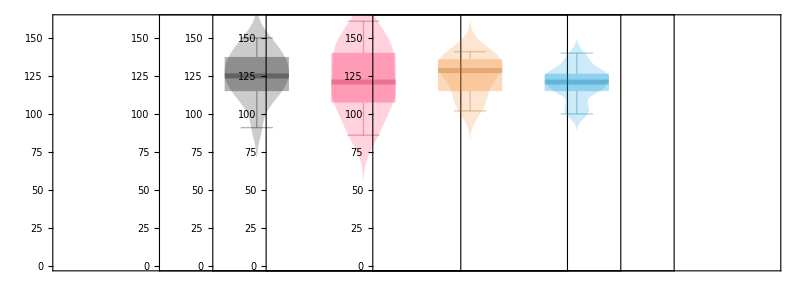

```mathematica
GraphicsRow[{controlCharts,v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```